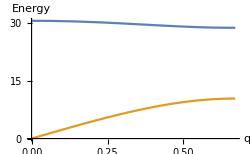

```mathematica
(*Carbon and Zirconium masses in AMU
M1=92
M2=12*)
(*ZrC lattice parameter in angstrom*)
a=4.685;
(*force constant in meV/Ang*)
fc=5000;
omegaminus[q_,M1_,M2_]:=(fc*(1/M1+1/M2)-fc*((1/M1+1/M2)^2-(4/(M1*M2))*Sin[q*a/2]^2)^0.5)^0.5
omegaplus[q_,M1_,M2_]:=(fc*(1/M1+1/M2)+fc*((1/M1+1/M2)^2-4/(M1*M2)*Sin[q*a/2]^2)^0.5)^0.5
Plot[{omegaplus[q,12,92],omegaminus[q,12,92]},{q,0,Pi/a},AxesLabel->{"q","Energy"},ImageSize->250]
```

```mathematica
1
```

```mathematica
omegaplusminus[q_,M1_,M2_]:={omegaminus[q,M1,M2],omegaplus[q,M1,M2]};
Manipulate[Show[Plot[{omegaminus[q,12,M2],omegaplus[q,12,M2]},{q,-Pi/a,Pi/a},ImageSize -> 500,PlotStyle->{{Thick},{Thick}},AxesLabel->{"q","\nEnergy"},PlotLegends->SwatchLegend[{"Acoustic","Optic"}],PlotLabel -> Row[{ Style["X-carbon diatomic linear chain phonon dispersion", Larger]}]] ],{{M2,92,"Mass of X (AMU)\nReference: Zr=92"},1,180,Appearance->"Labeled"},  ControllerLinking -> True,Initialization :> { Attributes[PlotRange] = {ReadProtected}}]
```

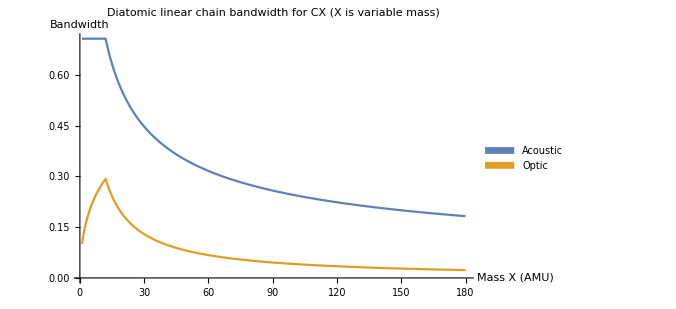

```mathematica
Opticwidth[M2_]:=Abs@(omegaplus[Pi/a,12,M2]-omegaplus[0,12,M2])
Acousticwidth[M2_]:=Abs@(omegaminus[Pi/a,12,M2]-omegaminus[0,12,M2])
Plot[{Acousticwidth[M2],Opticwidth[M2]},{M2,1,180},ImageSize -> 500,PlotStyle->{{Thick},{Thick}},AxesLabel->{"Mass X (AMU)","\nBandwidth"},PlotLegends->SwatchLegend[{"Acoustic","Optic"}],PlotLabel->"Diatomic linear chain bandwidth for CX\n (X is variable mass)"]
```

```mathematica
gradomegaminus[q_,M1_,M2_]=D[(fc*(1/M1+1/M2)-fc*((1/M1+1/M2)^2-(4/(M1*M2))*Sin[q*a/2]^2)^0.5)^0.5,q];
gradomegaplus[q_,M1_,M2_]=D[(fc*(1/M1+1/M2)-fc*((1/M1+1/M2)^2-(4/(M1*M2))*Sin[q*a/2]^2)^0.5)^0.5,q];
Manipulate[Show[ListPlot[{gradomegaminus[q,12,M2],gradomegaplus[q,12,M2]}/.q->Table[i,{i,0.01,0.2Pi,0.01}],Joined->True,ImageSize -> 500,PlotStyle->{{Thick},{Thick}},AxesLabel->{"Pi/a (Ang^-1)","\nEnergy (meV)"},PlotLegends->SwatchLegend[{"Acoustic","Optic"}],PlotLabel -> Row[{ Style["X-carbon diatomic linear chain phonon band velocity (gradient)", Larger]}]] ],{{M2,92,"Mass of X (AMU)\nReference: Zr=92"},1,180,Appearance->"Labeled"},  ControllerLinking -> True,Initialization :> { Attributes[PlotRange] = {ReadProtected}}]
```